We hebben eeen toppunt en een ander punt.  We gebruiken dus de vergelijking a (x-p)^2+q==y waarbij p = 28 (de dag) en q=327 (het aantal doden)

```mathematica
a(x-p)^2+q==y/.{p->28,q->327}
```

327+a (-28+x)^2==y

```mathematica
{1, 14} ligt op de curve
```

```mathematica
327+a (-28+x)^2==y/.{x->1,y->14}
```

327+729 a==14

```mathematica
Solve[327+729 a==14,a]
```

{{a→-313/729}}

Dus de curve was 327+a (-28+x)^2==y en dus

```mathematica
327+a (-28+x)^2==y/.{a->-313/729}
```

327-313/729 (-28+x)^2==y

```mathematica
Expand[327-313/729 (-28+x)^2==y]
```

-7009/729+(17528 x)/729-(313 x^2)/729==y

Nu moeten we de nulpunten van deze functie berekenen:

```mathematica
Solve[-7009/729+(17528 x)/729-(313 x^2)/729==0,x]
```

{{x→1/313 (8764-27 √102351)},{x→1/313 (8764+27 √102351)}}

```mathematica
NSolve[-7009/729+(17528 x)/729-(313 x^2)/729==0,x]
```

{{x→0.402771},{x→55.5972}}

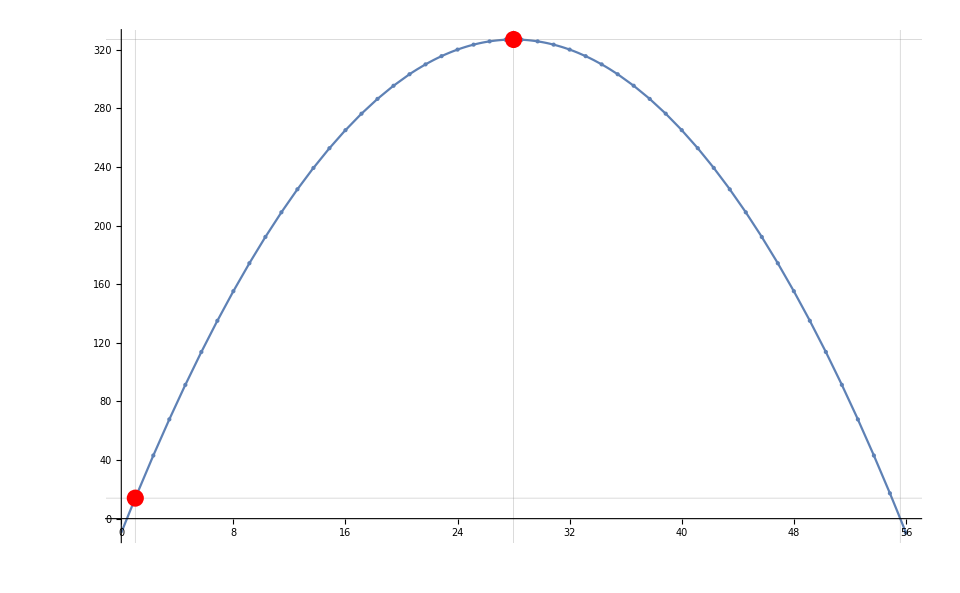

```mathematica
Show[Plot[-7009/729+(17528 x)/729-(313 x^2)/729,{x,0,56}, Mesh->Full, GridLines->{{1,28,55.59722864263718},{14,327}}],ListPlot[{{1,14},{28,327}}, PlotStyle->Red]]
```

```mathematica
-7009/729+(17528 x)/729-(313 x^2)/729/.x->1
```

14

```mathematica
-7009/729+(17528 x)/729-(313 x^2)/729/.x->28
```

327